## Initial setup

```mathematica
Remove["Global`*"]
```

```mathematica
e = 0.000000001;
maxDepth = 100;
```

## Point sampling (current example)

```mathematica
npoints =300;
sp = SpherePoints[npoints];
```

```mathematica
sn = sp;
```

```mathematica
plt1 = Show[
Table[Graphics3D[Arrow[{sp[[i]], sp[[i]]+sn[[i]]}]],{i,npoints}],
ListPointPlot3D[sp, AspectRatio->1]
];
```

## Octree spatial partition

```mathematica
initialWidth = Max[(Max@sp[[All,#]]&/@Range[3])-(Min@sp[[All,#]]&/@Range[3])] + 2.00 * e
```

1.99622

```mathematica
initialCenter = ((Max@sp[[All,#]]&/@Range[3])+(Min@sp[[All,#]]&/@Range[3]))/2.00
```

{0.000770428,0.00113568,0.}

```mathematica
{xmin, ymin, zmin} = initialCenter - initialWidth * 0.65;
{xmax, ymax, zmax} = initialCenter + initialWidth * 0.65;
```

```mathematica
(* { {{center}, width}, {idx1, idx2, idx3, ...} } *)
octree = {{{initialCenter, initialWidth},Table[i, {i,Length[sp]}]}};
```

```mathematica
SubdivideNode[node_, pts_]:=Module[{n, points, idx, center, width, child1, child2, child3, child4, child5, child6, child7, child8, result},
n=node;
points=pts;
idx = n[[2]];
center = n[[1]][[1]];
width = n[[1]][[2]];
(* Subdivide only if the node has more than 1 points *)
If[Length[idx]>1,
(* True: Subdivide *)
child1 = {};
child2 = {};
child3 = {};
child4 = {};
child5 = {};
child6 = {};
child7 = {};
child8 = {};
Do[ (* for each point in the node *)
If[points[[idx[[i]]]][[1]] ≤ center[[1]] && points[[idx[[i]]]][[2]] ≤ center[[2]] && points[[idx[[i]]]][[3]] ≤ center[[3]],child1 = Append[child1, idx[[i]]]];
If[points[[idx[[i]]]][[1]] > center[[1]] && points[[idx[[i]]]][[2]] ≤ center[[2]] && points[[idx[[i]]]][[3]] ≤ center[[3]],child2 = Append[child2, idx[[i]]]];
If[points[[idx[[i]]]][[1]] ≤ center[[1]] && points[[idx[[i]]]][[2]] > center[[2]] && points[[idx[[i]]]][[3]] ≤ center[[3]],child3 = Append[child3, idx[[i]]]];
If[points[[idx[[i]]]][[1]] > center[[1]] && points[[idx[[i]]]][[2]] > center[[2]] && points[[idx[[i]]]][[3]] ≤ center[[3]],child4 = Append[child4, idx[[i]]]];
If[points[[idx[[i]]]][[1]] ≤ center[[1]] && points[[idx[[i]]]][[2]] ≤ center[[2]] && points[[idx[[i]]]][[3]] > center[[3]],child5 = Append[child5, idx[[i]]]];
If[points[[idx[[i]]]][[1]] > center[[1]] && points[[idx[[i]]]][[2]] ≤ center[[2]] && points[[idx[[i]]]][[3]] > center[[3]],child6 = Append[child6, idx[[i]]]];
If[points[[idx[[i]]]][[1]] ≤ center[[1]] && points[[idx[[i]]]][[2]] > center[[2]] && points[[idx[[i]]]][[3]] > center[[3]],child7 = Append[child7, idx[[i]]]];
If[points[[idx[[i]]]][[1]] > center[[1]] && points[[idx[[i]]]][[2]] > center[[2]] && points[[idx[[i]]]][[3]] > center[[3]],child8 = Append[child8, idx[[i]]]]
,{i,Length[idx]}];
(* Construct what to return *)
result = {};
If[Length[child1]>0, result=Append[result,{{center+{-width/4.0, -width/4.0, -width/4.0}, width/2.0},child1}]];
If[Length[child2]>0, result=Append[result,{{center+{+width/4.0, -width/4.0, -width/4.0}, width/2.0},child2}]];
If[Length[child3]>0, result=Append[result,{{center+{-width/4.0, +width/4.0, -width/4.0}, width/2.0},child3}]];
If[Length[child4]>0, result=Append[result,{{center+{+width/4.0, +width/4.0, -width/4.0}, width/2.0},child4}]];
If[Length[child5]>0, result=Append[result,{{center+{-width/4.0, -width/4.0, +width/4.0}, width/2.0},child5}]];
If[Length[child6]>0, result=Append[result,{{center+{+width/4.0, -width/4.0, +width/4.0}, width/2.0},child6}]];
If[Length[child7]>0, result=Append[result,{{center+{-width/4.0, +width/4.0, +width/4.0}, width/2.0},child7}]];
If[Length[child8]>0, result=Append[result,{{center+{+width/4.0, +width/4.0, +width/4.0}, width/2.0},child8}]];
n = result;,
(* else *)
n = {n};
]; (* end if *)
n] (* end function *)
```

```mathematica
(*SubdivideNode[node_, pts_]:=Module[{n, points, idx, center, width, child1, child2, child3, child4, child5, child6, child7, child8, result},
n=node;
points=pts;
idx = n[[2]];
center = n[[1]][[1]];
width = n[[1]][[2]];

child1 = {};
child2 = {};
child3 = {};
child4 = {};
child5 = {};
child6 = {};
child7 = {};
child8 = {};
Do[ (* for each point in the node *)
If[points[[idx[[i]]]][[1]] ≤ center[[1]] && points[[idx[[i]]]][[2]] ≤ center[[2]] && points[[idx[[i]]]][[3]] ≤ center[[3]],child1 = Append[child1, idx[[i]]]];
If[points[[idx[[i]]]][[1]] > center[[1]] && points[[idx[[i]]]][[2]] ≤ center[[2]] && points[[idx[[i]]]][[3]] ≤ center[[3]],child2 = Append[child2, idx[[i]]]];
If[points[[idx[[i]]]][[1]] ≤ center[[1]] && points[[idx[[i]]]][[2]] > center[[2]] && points[[idx[[i]]]][[3]] ≤ center[[3]],child3 = Append[child3, idx[[i]]]];
If[points[[idx[[i]]]][[1]] > center[[1]] && points[[idx[[i]]]][[2]] > center[[2]] && points[[idx[[i]]]][[3]] ≤ center[[3]],child4 = Append[child4, idx[[i]]]];
If[points[[idx[[i]]]][[1]] ≤ center[[1]] && points[[idx[[i]]]][[2]] ≤ center[[2]] && points[[idx[[i]]]][[3]] > center[[3]],child5 = Append[child5, idx[[i]]]];
If[points[[idx[[i]]]][[1]] > center[[1]] && points[[idx[[i]]]][[2]] ≤ center[[2]] && points[[idx[[i]]]][[3]] > center[[3]],child6 = Append[child6, idx[[i]]]];
If[points[[idx[[i]]]][[1]] ≤ center[[1]] && points[[idx[[i]]]][[2]] > center[[2]] && points[[idx[[i]]]][[3]] > center[[3]],child7 = Append[child7, idx[[i]]]];
If[points[[idx[[i]]]][[1]] > center[[1]] && points[[idx[[i]]]][[2]] > center[[2]] && points[[idx[[i]]]][[3]] > center[[3]],child8 = Append[child8, idx[[i]]]]
,{i,Length[idx]}];
(* Construct what to return *)
result = {};
If[Length[child1]>0, result=Append[result,{{center+{-width/4.0, -width/4.0, -width/4.0}, width/2.0},child1}]];
If[Length[child2]>0, result=Append[result,{{center+{+width/4.0, -width/4.0, -width/4.0}, width/2.0},child2}]];
If[Length[child3]>0, result=Append[result,{{center+{-width/4.0, +width/4.0, -width/4.0}, width/2.0},child3}]];
If[Length[child4]>0, result=Append[result,{{center+{+width/4.0, +width/4.0, -width/4.0}, width/2.0},child4}]];
If[Length[child5]>0, result=Append[result,{{center+{-width/4.0, -width/4.0, +width/4.0}, width/2.0},child5}]];
If[Length[child6]>0, result=Append[result,{{center+{+width/4.0, -width/4.0, +width/4.0}, width/2.0},child6}]];
If[Length[child7]>0, result=Append[result,{{center+{-width/4.0, +width/4.0, +width/4.0}, width/2.0},child7}]];
If[Length[child8]>0, result=Append[result,{{center+{+width/4.0, +width/4.0, +width/4.0}, width/2.0},child8}]];
n = result;
n] (* end function *)  *)
```

```mathematica
SubdivideOctree[oct_, pts_]:=Module[{tr, points, output, result},
tr=oct;
points=pts;
output = {};
Do[
result =SubdivideNode[tr[[i]],points];
 Do[output = Append[output,result[[j]]],{j,Length[result]}],
{i, Length[tr]}
];
output
]
```

```mathematica
octree;
```

```mathematica
Do[octree = SubdivideOctree[octree, sp], {i,maxDepth}]
```

```mathematica
nleaves = Length[octree]
```

300

```mathematica
octree;
```

## System

```mathematica
F[q_]:=(2π)^(-3/2)*Exp[-1/2 qᵀ.q]
```

```mathematica
Fo[q_,c_,w_]:=F[1/w*(q-c)]
```

```mathematica
(* Gradient field *)
```

```mathematica
V[q_]:=Sum[
Sum[
Fo[
q,
 octree[[i]][[1]][[1]], (* leaf i center *)
octree[[i]][[1]][[2]] (* leaf i width *)
]
 * sn[[  
octree[[i]][[2]][[j]]  (* j-th index of contents of leaf i *)
 ]],
{j, Length[ octree[[i]][[2]]]}], (* iterate over the contents of leaf i *)
{i,nleaves}] (* iterate over leaves *)
```

```mathematica
(* VectorPlot3D[V[{x,y,z}],{x,xmin,xmax},{y,ymin,ymax},{z,zmin,zmax}, VectorScaling-> Automatic]; *)
```

```mathematica
dFox[{x_,y_,z_},{cx_,cy_,cz_},w_] = D[Fo[{x,y,z},{cx,cy,cz},w],x];
dFoy[{x_,y_,z_},{cx_,cy_,cz_},w_] = D[Fo[{x,y,z},{cx,cy,cz},w],y];
dFoz[{x_,y_,z_},{cx_,cy_,cz_},w_] = D[Fo[{x,y,z},{cx,cy,cz},w],z];
```

```mathematica
(* symbolic divergance of vector field *)
divV[{x_,y_,z_}]=Sum[
Sum[
{dFox[
{x,y,z},
 octree[[i]][[1]][[1]], (* leaf i center *)
octree[[i]][[1]][[2]] (* leaf i width *)
] ,
dFoy[
{x,y,z},
 octree[[i]][[1]][[1]], (* leaf i center *)
octree[[i]][[1]][[2]] (* leaf i width *)
],
dFoz[
{x,y,z},
 octree[[i]][[1]][[1]], (* leaf i center *)
octree[[i]][[1]][[2]] (* leaf i width *)
]}ᵀ
 . sn[[  
octree[[i]][[2]][[j]]  (* j-th index of contents of leaf i *)
 ]] 
,
{j, Length[ octree[[i]][[2]]]}], (* iterate over the contents of leaf i *)
{i,nleaves}];(* iterate over leaves *)
```

```mathematica
(* Fxo1o2[{c1x_,c1y_,c1z_},{c2x_,c2y_,c2z_},w1_,w2_]=Integrate[dFox[{x,y,z},{c1x,c1y,c1z},w1]*Fo[{x,y,z},{c2x, c2y, c2z}, w2],
{x,-Infinity,Infinity},
 {y,-Infinity,Infinity},
{z,-Infinity,Infinity},
Assumptions-> {c1x∈Reals,c1y∈Reals,c1z∈Reals,c2x∈Reals,c2y∈Reals,c2z∈Reals,w1∈Reals, w2∈Reals, w1>0, w2>0}] *)
```

```mathematica
(* This is the result we get, it takes too long to get it: *)
Fxo1o2[{c1x_,c1y_,c1z_},{c2x_,c2y_,c2z_},w1_,w2_]=((c1x-c2x) ⅇ^(-(c1x^2+c1y^2+c1z^2-2 c1x c2x+c2x^2-2 c1y c2y+c2y^2-2 c1z c2z+c2z^2)/(2 (w1^2+w2^2))) w1^3 w2^3)/(2 √2 π^(3/2) (w1^2+w2^2)^(5/2));
```

```mathematica
(* Fyo1o2[{c1x_,c1y_,c1z_},{c2x_,c2y_,c2z_},w1_,w2_]=Once[
Integrate[dFoy[{x,y,z},{c1x,c1y,c1z},w1]*Fo[{x,y,z},{c2x, c2y, c2z}, w2],
{x,-Infinity,Infinity},
 {y,-Infinity,Infinity},
{z,-Infinity,Infinity},
Assumptions-> {c1x∈Reals,c1y∈Reals,c1z∈Reals,c2x∈Reals,c2y∈Reals,c2z∈Reals,w1∈Reals, w2∈Reals, w1>0, w2>0}],
"Fyo1o2"] *)
```

```mathematica
Fyo1o2[{c1x_,c1y_,c1z_},{c2x_,c2y_,c2z_},w1_,w2_] = ((c1y-c2y) ⅇ^(-(c1x^2+c1y^2+c1z^2-2 c1x c2x+c2x^2-2 c1y c2y+c2y^2-2 c1z c2z+c2z^2)/(2 (w1^2+w2^2))) w1^3 w2^3)/(2 √2 π^(3/2) (w1^2+w2^2)^(5/2));
```

```mathematica
(* Fzo1o2[{c1x_,c1y_,c1z_},{c2x_,c2y_,c2z_},w1_,w2_]=Once[
Integrate[dFoz[{x,y,z},{c1x,c1y,c1z},w1]*Fo[{x,y,z},{c2x, c2y, c2z}, w2],
{x,-Infinity,Infinity},
 {y,-Infinity,Infinity},
{z,-Infinity,Infinity},
Assumptions-> {c1x∈Reals,c1y∈Reals,c1z∈Reals,c2x∈Reals,c2y∈Reals,c2z∈Reals,w1∈Reals, w2∈Reals, w1>0, w2>0}],
"Fzo1o2"] *)
```

```mathematica
Fzo1o2[{c1x_,c1y_,c1z_},{c2x_,c2y_,c2z_},w1_,w2_] =((c1z-c2z) ⅇ^(-(c1x^2+c1y^2+c1z^2-2 c1x c2x+c2x^2-2 c1y c2y+c2y^2-2 c1z c2z+c2z^2)/(2 (w1^2+w2^2))) w1^3 w2^3)/(2 √2 π^(3/2) (w1^2+w2^2)^(5/2));
```

```mathematica
v = ParallelTable[
Sum[ (* for every other leaf j *)
(* i: the leaf that corresponds to the element of v we are calculating *)
(* j: any other leaf, i included *)
(* octree[[j]][[2]][[k]]: the k-th index of the contents of leaf node j *)
(* sn[[  octree[[j]][[2]][[k]]  ]]: the normal vector of the corresponding sample point *) 
(* octree[[i]][[1]][[1]]: the center of leaf node i *)
(* octree[[j]][[1]][[1]]: the center of leaf node j *)
(* octree[[i]][[1]][[2]]: the width of leaf node i *)
(* octree[[j]][[1]][[2]]: the width of leaf node j *)
Sum[ (* for every sample in leaf j *)
{Fxo1o2[octree[[j]][[1]][[1]],octree[[i]][[1]][[1]],octree[[j]][[1]][[2]],octree[[i]][[1]][[2]]],
Fyo1o2[octree[[j]][[1]][[1]],octree[[i]][[1]][[1]],octree[[j]][[1]][[2]],octree[[i]][[1]][[2]]],
Fzo1o2[octree[[j]][[1]][[1]],octree[[i]][[1]][[1]],octree[[j]][[1]][[2]],octree[[i]][[1]][[2]]]}ᵀ.sn[[  octree[[j]][[2]][[  k  ]]  ]]
,
{k,Length[octree[[j]][[2]]]}]
,
{j, nleaves}]
,
{i,nleaves}];
```

```mathematica
(* Fxxo1o2 = Integrate[D[Fo[{x,y,z},{c1x,c1y,c1z},w1],x,x] * Fo[{x,y,z},{c2x,c2y,c2z},w2],
{x,-Infinity,Infinity},
{y,-Infinity,Infinity},
{z,-Infinity,Infinity},
Assumptions-> {c1x∈Reals,c1y∈Reals,c1z∈Reals,c2x∈Reals,c2y∈Reals,c2z∈Reals,w1∈Reals, w2∈Reals, w1>0, w2>0}] *)
```

```mathematica
cf=Compile[{{x,_Real}},Sin[x]+x^2-1/(1+x)]
```

CompiledFunction[…]

```mathematica
cf[0.20]
```

-0.594664

```mathematica
Fxxo1o2 = Compile[{{c1x, _Real},{c1y, _Real},{c1z, _Real},{c2x, _Real},{c2y, _Real},{c2z, _Real},{w1, _Real},{w2, _Real}},-(ⅇ^(-(c1x^2+c1y^2+c1z^2-2 c1x c2x+c2x^2-2 c1y c2y+c2y^2-2 c1z c2z+c2z^2)/(2 (w1^2+w2^2))) w1^3 w2^3 (-c1x^2+2 c1x c2x-c2x^2+w1^2+w2^2))/(2 √2 π^(3/2) (w1^2+w2^2)^(7/2)),
CompilationTarget->"C"]
```

CompiledFunction[…]

```mathematica
(* Integrate[D[Fo[{x,y,z},{c1x,c1y,c1z},w1],y,y] * Fo[{x,y,z},{c2x,c2y,c2z},w2],
{x,-Infinity,Infinity},
{y,-Infinity,Infinity},
{z,-Infinity,Infinity},
Assumptions-> {c1x∈Reals,c1y∈Reals,c1z∈Reals,c2x∈Reals,c2y∈Reals,c2z∈Reals,w1∈Reals, w2∈Reals, w1>0, w2>0}] *)
```

```mathematica
Fyyo1o2 = Compile[{{c1x, _Real},{c1y, _Real},{c1z, _Real},{c2x, _Real},{c2y, _Real},{c2z, _Real},{w1, _Real},{w2, _Real}},-(ⅇ^(-(c1x^2+c1y^2+c1z^2-2 c1x c2x+c2x^2-2 c1y c2y+c2y^2-2 c1z c2z+c2z^2)/(2 (w1^2+w2^2))) w1^3 w2^3 (-c1y^2+2 c1y c2y-c2y^2+w1^2+w2^2))/(2 √2 π^(3/2) (w1^2+w2^2)^(7/2)),
CompilationTarget->"C"]
```

CompiledFunction[…]

```mathematica
(* Integrate[D[Fo[{x,y,z},{c1x,c1y,c1z},w1],z,z] * Fo[{x,y,z},{c2x,c2y,c2z},w2],
{x,-Infinity,Infinity},
{y,-Infinity,Infinity},
{z,-Infinity,Infinity},
Assumptions-> {c1x∈Reals,c1y∈Reals,c1z∈Reals,c2x∈Reals,c2y∈Reals,c2z∈Reals,w1∈Reals, w2∈Reals, w1>0, w2>0}] *)
```

```mathematica
Fzzo1o2 = Compile[{{c1x, _Real},{c1y, _Real},{c1z, _Real},{c2x, _Real},{c2y, _Real},{c2z, _Real},{w1, _Real},{w2, _Real}},(ⅇ^(-(c1x^2+c1y^2+c1z^2-2 c1x c2x+c2x^2-2 c1y c2y+c2y^2-2 c1z c2z+c2z^2)/(2 (w1^2+w2^2))) w1^3 w2^3 (c1z^2-2 c1z c2z+c2z^2-w1^2-w2^2))/(2 √2 π^(3/2) (w1^2+w2^2)^(7/2)),
CompilationTarget->"C"]
```

CompiledFunction[…]

```mathematica
L=ParallelTable[
Total[{
Fxxo1o2[
octree[[i]][[1]][[1]][[1]],
octree[[i]][[1]][[1]][[2]],
octree[[i]][[1]][[1]][[3]],
octree[[j]][[1]][[1]][[1]],
octree[[j]][[1]][[1]][[2]],
octree[[j]][[1]][[1]][[3]],
octree[[i]][[1]][[2]],
octree[[j]][[1]][[2]]
],
Fyyo1o2[
octree[[i]][[1]][[1]][[1]],
octree[[i]][[1]][[1]][[2]],
octree[[i]][[1]][[1]][[3]],
octree[[j]][[1]][[1]][[1]],
octree[[j]][[1]][[1]][[2]],
octree[[j]][[1]][[1]][[3]],
octree[[i]][[1]][[2]],
octree[[j]][[1]][[2]]
],
Fzzo1o2[
octree[[i]][[1]][[1]][[1]],
octree[[i]][[1]][[1]][[2]],
octree[[i]][[1]][[1]][[3]],
octree[[j]][[1]][[1]][[1]],
octree[[j]][[1]][[1]][[2]],
octree[[j]][[1]][[1]][[3]],
octree[[i]][[1]][[2]],
octree[[j]][[1]][[2]]]
}]
,
{i,nleaves},{j,nleaves}];
```

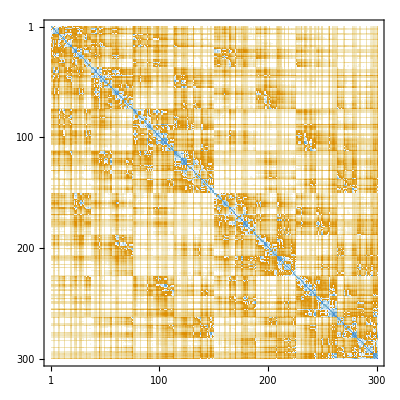

```mathematica
MatrixPlot[L]
```

```mathematica
L//MatrixForm;
```

```mathematica
xvec = LinearSolve[L,v];
```

```mathematica
chi[q_]:=Sum[
xvec[[i]] * Fo[q,octree[[i]][[1]][[1]],octree[[i]][[1]][[2]]]
,{i,nleaves}]
```

```mathematica
γ = Mean[ParallelTable[chi[sp[[i]]],{i,npoints}]];
```

## Visualization

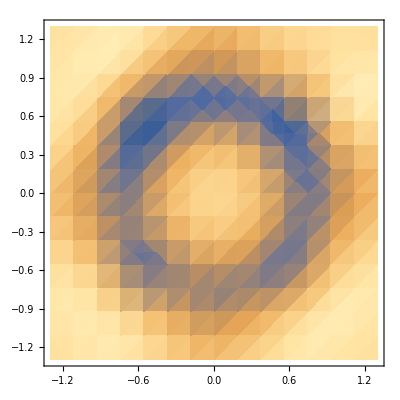

```mathematica
DensityPlot[chi[{x,y,0.00}]==γ,{x,xmin,xmax},{y,ymin,ymax}]
```

Warning: Heavy

```mathematica
(* cp = ContourPlot3D[chi[{x,y,z}]==γ,{x,xmin,xmax},{y,ymin,ymax},{z,zmin,zmax},Mesh-> None,  ContourStyle-> {Green, Opacity[0.2]}] *)
```